```mathematica
Clear["GLobals`*"]
```

----- Creamos una funcion ------
 Module [ { Inicializamos los valores separados por comas } , Funcion [ ] : = Escribimos la funcion ]

```mathematica
Module[{a=314159269,c=453806245,m=2^31,z=1000},RndData[]:= (z=Mod[z*a+c,m])/m //N
]
```

```mathematica
RndData[]
```

0.257517

----- Recogemos muestras -----

```mathematica
muestras =Table[RndData[],20];
```

```mathematica
muestras[[1;;20]]
```

{0.712859,0.713201,0.914167,0.569745,0.199669,0.0487442,0.337575,0.605346,0.999724,0.556968,0.1385,0.478027,0.632218,0.766075,0.589344,0.79221,0.430469,0.253651,0.704795,0.598373}

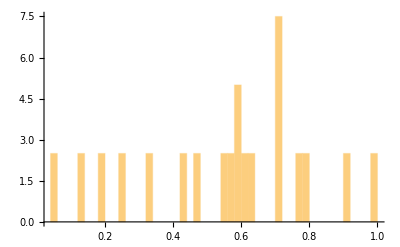

```mathematica
Histogram[muestras,30,PDF]
```

Creamos la funcion exponencial

```mathematica
RndExp[rate_]:=-Log[RndData[]]/rate;
```

```mathematica
muestras2=Table[RndExp[100],10000];
muestras2[[1;;20]]
```

{0.0363164,0.00994463,0.00046924,0.00123699,0.00374398,0.00294371,0.0113138,0.000651825,0.00472428,0.0359129,0.000311348,0.0274336,0.0232572,0.0153869,0.00701796,0.000233459,0.0146007,0.0248212,0.0109974,0.00206558}

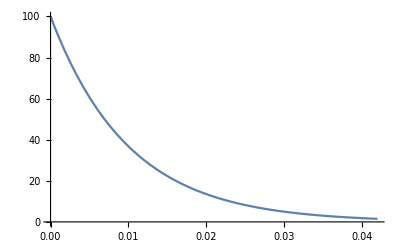

```mathematica
g1=Plot[100*E^(-100*t),{t,0,0.042}]
```

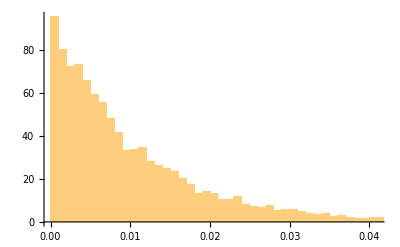

```mathematica
h1=Histogram[muestras2,100,PDF]
```

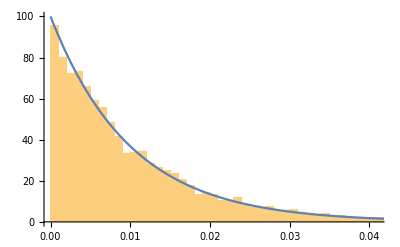

```mathematica
Show [h1,g1]
```

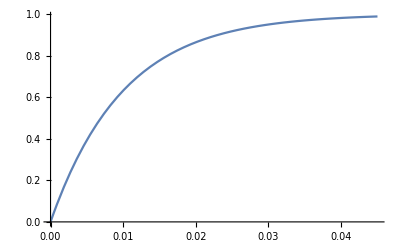

```mathematica
g=Plot[1-E^(-100*t),{t,0,0.045}]
```

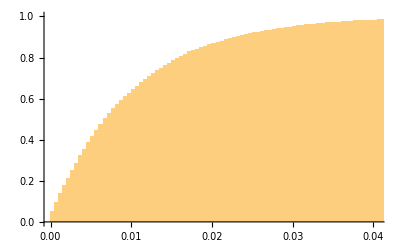

```mathematica
h=Histogram[muestras2,200,CDF]
```

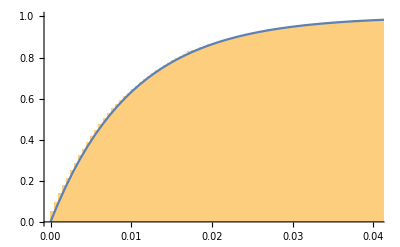

```mathematica
Show[h,g]
```